```mathematica
(*wipeAll[]*)
```

```mathematica
SetDirectory@NotebookDirectory[];
<<"MathUtils.wl"
(*<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,siunitx}"}];*)
```

/home/bryan/Documents/Base/Homework/ThermalFieldTheory2020/thermal5/plots/spectral.nb

```mathematica
q=(2w-k^2)/(2k);
e=q^2/2;
rho[w_,k_,t_,u_]=(-Sign[q]t)/k Log[(1+E^(-(e-u)/t))/(1+E^(-(e-u+w)/t))];
Manipulate[
Quiet[
Plot[rho[w,k,t,u],{w,0,5},PlotRange->All,Exclusions->None]
]
,{{{t,1},.01,10,#},{{u,1},-5,5,#},{{k,1},0,20,#}}&[
Appearance->"Open"
]//Apply[Sequence]//Evaluate
]
```

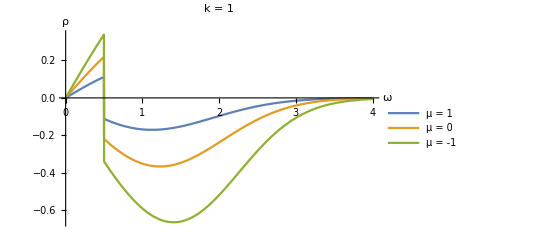

./spectralmu.pdf

```mathematica
spectralmu=Plot[{
rho[w,1,1,-1],
rho[w,1,1,0],
rho[w,1,1,1]
},{w,0,4}
,PlotRange->All,Exclusions->None
,PlotLegends->Evaluate[Style[#,12]&/@{
"μ = 1",
"μ = 0",
"μ = -1"
}]
,AxesLabel->{ω,ρ}
,PlotLabel->"k = 1"
]
exportPlot[spectralmu,"./"]
```

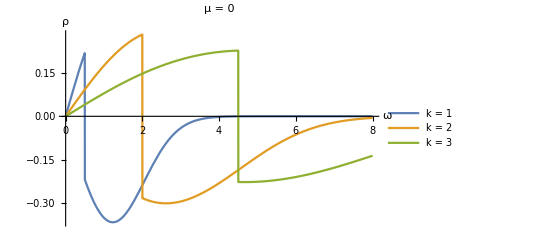

./spectralk.pdf

```mathematica
spectralk=Plot[{
rho[w,1,1,0],
rho[w,2,1,0],
rho[w,3,1,0]
},{w,0,8}
,PlotRange->All,Exclusions->None
,PlotLegends->Evaluate[Style[#,12]&/@{
"k = 1",
"k = 2",
"k = 3"
}]
,AxesLabel->{ω,ρ}
,PlotLabel->"μ = 0"
]
exportPlot[spectralk,"./"]
```